```mathematica
link = Install[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"bin","FreewayAC_Mathematica"}]]
```

LinkObject[…]

```mathematica
Column@LinkPatterns[link]
```

CreateCircularCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer]
CreateOpenCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,newCarProb_Real,newCarSpeed]
CreateCircularCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,autDensity_Real]
DeleteCA[]
CAStep[]
CAEvolve[iterations_Integer]
CACountCars[]
CACalculateOcupancy[]
CACalculateFlow[]
CAGetCurrent[]
CAGetHistory[]

```mathematica
CreateCircularCA[100,5,0.5,0.2,1]
CAEvolve[100]
```

```mathematica
ca = CAGetHistory[]
```

{{1,1,1,-1,-1,-1,-1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,1,-1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,1,1,-1,1,-1,-1,1,-1,1,-1,1,-1,-1,1,1,1,1,1,-1,-1,-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,1,1,1,1,-1,1,-1,-1,1,-1,-1,1,-1,-1,1,-1,-1,1,1,-1,-1,1},99,{0,0,-1,94,0,0,0}}
 |  |  |  |

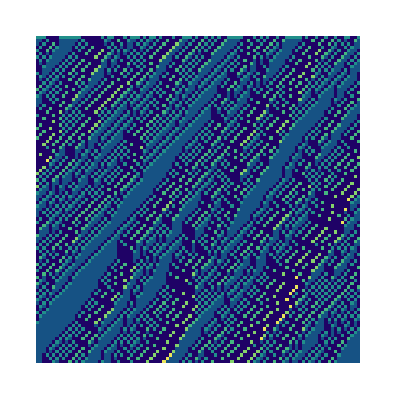

```mathematica
ArrayPlot[ca,ColorFunction->"BlueGreenYellow"]
```

```mathematica
CAGetCurrent[]
```

{-1,1,0,-1,-1,1,-1,-1,2,-1,-1,-1,-1,2,-1,0,0,-1,1,0,-1,1,0,-1,1,-1,1,-1,-1,-1,2,-1,-1,2,-1,-1,-1,3,-1,-1,-1,3,-1,-1,1,0,-1,0,0,-1,1,-1,-1,2,-1,1,-1,1,0,0,-1,-1,0,0,-1,0,0,-1,0,-1,1,-1,1,-1,1,-1,1,0,-1,1,-1,1,0,-1,1,0,0,0,-1,1,-1,1,0,0,-1,-1,-1,2,0,-1}